```mathematica
CloseKernels[];
LaunchKernels[7];spcs={"scerevisiae","celegans","dmelanogaster","drerio","trubripes","xtropicalis","ggallus","mmusculus","sscrofa","mmulatta","hsapiens"}
name={"s. cerevisiae","c. elegans","d. melanogaster","d. rerio","t. rubripes","x. tropicalis","g. gallus","m. musculus","s. scrofa","m. mulatta","h. sapiens" }
(*spcs={"mmusculus","celegans","dmelanogaster"}*)
```

{scerevisiae,celegans,dmelanogaster,drerio,trubripes,xtropicalis,ggallus,mmusculus,sscrofa,mmulatta,hsapiens}

{s. cerevisiae,c. elegans,d. melanogaster,d. rerio,t. rubripes,x. tropicalis,g. gallus,m. musculus,s. scrofa,m. mulatta,h. sapiens}

```mathematica
(*only the eleven*)
loca="/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/submission01-2019-09/SourceFiles/data/ensembl_data"
genel=Table[(*Import["/Users/abouchakra/Dropbox/Uoft/UOFT/projects/5-Gene_Length_pathway/3-R_directpathwayfiles_mathematica/data/pathway_overlaps_"<>spcs[[i]]<>"/"<>spcs[[i]]<>"_gene_ensembl_genesandtranslength.dat",RecordSeparators->"\t"],*)
Import[loca<>"/"<>spcs[[i]]<>"_gene_ensembl_genesandtranslength.txt"(*"_gene_ensembl_genelength.txt"*),"Data",RecordSeparators->"\t"],{i,Length[spcs]}];
```

/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/submission01-2019-09/SourceFiles/data/ensembl_data

90000

{0.,0.00494486,0.803905,7.33345,0.428314,4.88699,6.58347,12.6919,15.2456,16.751,18.964}

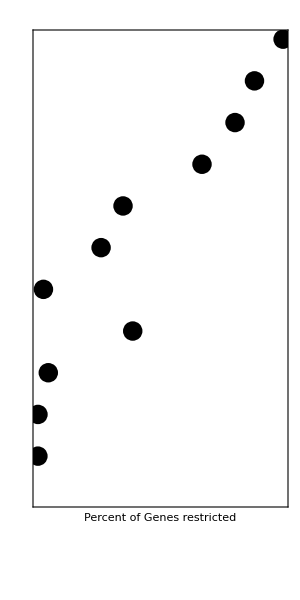

```mathematica
timeCC=((1500*60)) (*gene length transcribed in one hour*)
(*select for genes greater than timeCC*)
geneLengths=(Union/@genel[[All,1;;All,{1,-2}]])[[All,All,2]];
gN=Table[(Length[Select[geneLengths[[i]], #>timeCC&]])/Length[geneLengths[[i]]]//N,{i,1,11}]*100
lp=ListPlot[Transpose[{gN,Range[1,11]}],AspectRatio->2,Axes->False,Frame->True,FrameStyle->Directive[FontSize->20,Black],FrameTicks->None,FrameLabel->{{None,None},{"Percent of \n Genes restricted",None}},BaseStyle->{20,"Helvetica",Black},PlotMarkers->{Automatic,20},ImageSize->300]


(*BarChart[{Take[gN,7],Take[gN,-5]},BarOrigin->Left]*)
```

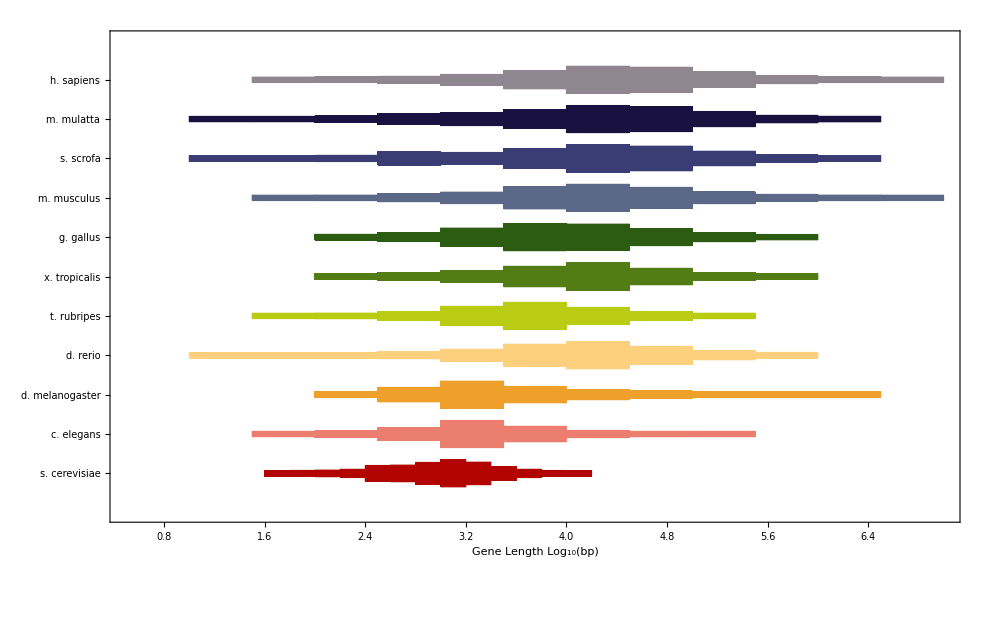

```mathematica
d=DistributionChart[Log[10,#]&/@geneLengths,PlotRange->{{0.5,7},{0,12}},Frame->True,(*FrameTicks->{{Automatic},{Automatic}},*)FrameLabel->{"Gene Length Log_10(bp)"," "},
BaseStyle->{FontFamily->"Helvetica",32,Black},FrameStyle->Directive[FontSize->25,Opacity[1],Black],ImagePadding->{{300,Automatic},{Automatic,Automatic}},(*PlotLabel->SwatchLegend[Reverse[ColorData[10][#]&/@Range[10,11]],{"Slow",(*"","","","","","","","","",*)"Fast"},(*LegendLabel->"Developmental Rate",*)LegendLayout->"Row"],*) ChartLabels->Placed[{name(*,Reverse[term]*)},{Axis(*,After*)}],ChartStyle->ColorData[10](*{ColorData[10][10],ColorData[10][10],ColorData[10][10],ColorData[10][10],ColorData[10][10],ColorData[10][10],ColorData[10][11],ColorData[10][11],ColorData[10][11],ColorData[10][11],ColorData[10][11]}*),
BarOrigin->Left,BaseStyle->{FontFamily->"Helvetica",44},ChartElementFunction->"HistogramDensity",ImageSize->1000]
```

```mathematica
Export["/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/manuscript_prep/Figure_distribution.pdf",d]
```

/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/manuscript_prep/Figure_distribution.pdf

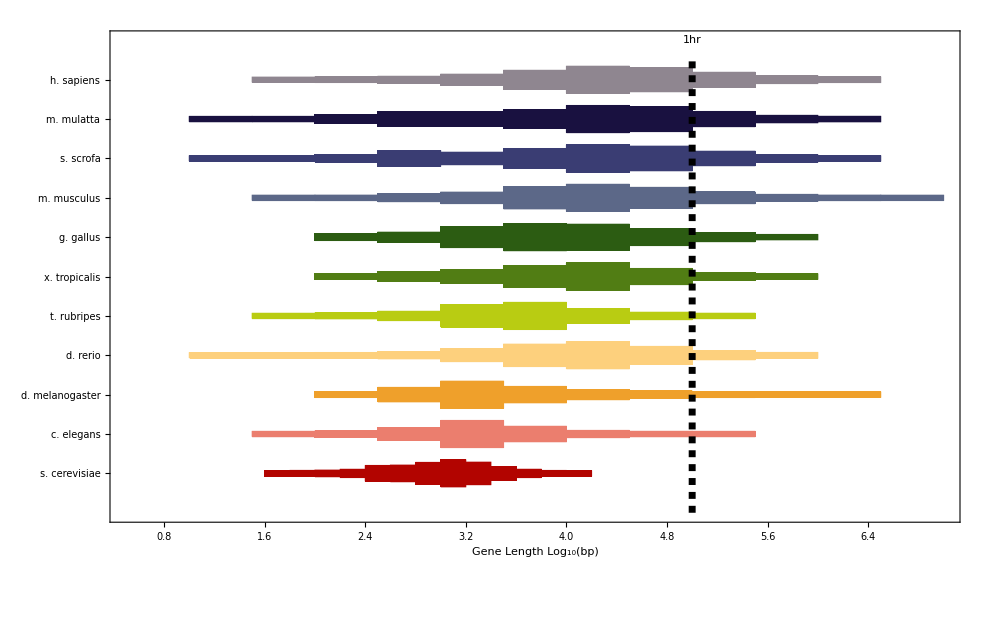

```mathematica
dL=Show[d,Graphics[{Dashed,Thickness[0.005],Black,Line[{{5,0},{5,11.5}}]}],Epilog->Text[Style["1hr",Black],{5.0,12.},Center],ImageSize->1000,BaseStyle->{FontFamily->"Helvetica",25,Black},FrameStyle->Directive[{Black,FontFamily->"Helvetica",25}]]
```

```mathematica
Export["/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/manuscript_prep/Figure_2d_distributionL1.nb",dL]
```

/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/manuscript_prep/Figure_2d_distributionL1.nb

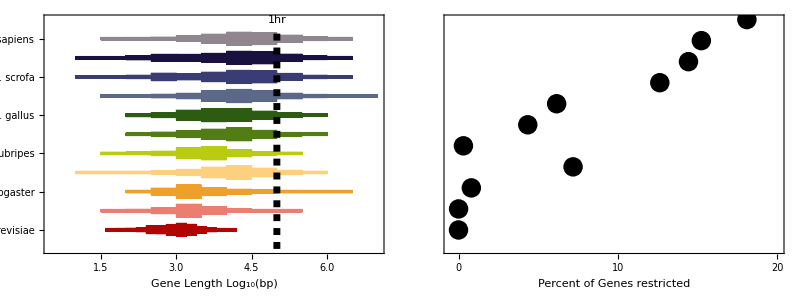

```mathematica
tal=TableForm[{{dL,Show[lp,ImageSize->190,Frame->True,PlotRange->{{-0.5,20},{0.1,11}},FrameTicks->{{None,None},{Range[0,20,10],Range[0,20,10]}}]}}]
```

```mathematica
Export["/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/submission01-2019-09/4-Figure_Genome_distributionL12.pdf",tal]
```

/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/submission01-2019-09/4-Figure_Genome_distributionL12.pdf

```mathematica
"/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/submission01-2019-09/4-Figure_Genome_distributionL12.pdf"
```

/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/submission01-2019-09/4-Figure_Genome_distributionL12.pdf